## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "windows";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\FKO";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

SetDirectory::cdir: Cannot set current directory to "~/repos/fp/FKO/data-plots".

For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames[[i]]]]

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->800];
```

#### variables

```mathematica
begin=350;end=14898;average=0.03;
```

Manipulate[ListPlot[data[n], PlotRange -> {0.95, 1.05}], {n, 0, 22, 1}]

#### Samples

Reflexion GK 300-8000

```mathematica
rgk=Table[ListPlot[data[n],PlotStyle->Blue],{n,7,10,1}];
```

Reflexion TQ 1000-15000

```mathematica
rtq=Table[ListPlot[data[n],PlotStyle->Red],{n,15,18,1}];
```

Transmission GK 300-8000

```mathematica
tgk=Table[ListPlot[data[n],PlotStyle->Darker[Blue]],{n,11,14,1}];
```

Reflexion TQ 1000-15000

```mathematica
ttq=Table[ListPlot[data[n],PlotStyle->Darker[Red]],{n,19,22,1}];
```

```mathematica
Manipulate[
temp=MovingAverage[data[9]⟦All,2⟧,u];
geglaettet=Flatten[{Table[temp[[1]],{i,1,(u-1)/2}],temp,Table[temp[[-1]],{u,1,(u-1)/2}]}];
ListPlot[Transpose[{data[9]⟦All,1⟧,geglaettet}], PlotRange->{0.4,0.48}],{u,1,101,2}]
```

#### Composed Plots of both sources

```mathematica
Manipulate[Show[{rgk⟦im⟧,rtq⟦im⟧}],{im,1,4,1},{e,0.1,10}]
```

```mathematica
geglaettety[n_]:=Flatten[{Table[MovingAverage[data[n]⟦All,2⟧,11][[1]],{i,1,(11-1)/2}],MovingAverage[data[n]⟦All,2⟧,11],Table[MovingAverage[data[n]⟦All,2⟧,11][[-1]],{u,1,(11-1)/2}]}];
```

```mathematica
Dimensions[data[9]⟦All,1⟧]
```

{3811}

```mathematica
Dimensions[Transpose[{data[9]⟦All,1⟧,geglaettety[9]}]]
```

{3811,2}

#### Connect functions

```mathematica
fctab=Table[Interpolation[Transpose[{data[n]⟦All,1⟧,geglaettety[n]}],InterpolationOrder->1],{n,1,Length[fnames]-1}];
```

```mathematica
fct[n_,cut_,x_:x]:=Piecewise[{{fctab⟦n⟧[x], x<cut}, {fctab⟦n+8⟧[x], x>cut}}]
```

```mathematica
Manipulate[Plot[{fctab⟦n⟧[x],fctab⟦n+8⟧[x],fct[n,cut,x]},{x,500,12000},PlotRange->Full],{n,0,14,1},{cut,1000,10000}]
```

```mathematica
cuts={{7,4100},{8,3930},{9,3200},{10,2100},{11,3000},{12,2200},{13,4000},{14,3000}};
```

## Analysis

#### reflexion and transmission functions

```mathematica
reflex[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,1,4}]⟦n-6⟧
```

```mathematica
trans[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,5,8}]⟦n-6⟧
```

```mathematica
Manipulate[Plot[trans[n,x],{x,301,12000},PlotRange->Full],{n,7,10,1}]
```

```mathematica
Δrg1=0.0;Δrg2=0.0;
```

```mathematica
(*Reflexion einer idealen Grenzfläche in Abhängigkeit von n und κ*)
rg[n_,κ_]:=((n-1)^2+κ^2)/((n+1)^2+κ^2);
```

```mathematica
(*Absorptionskoeffizient*)
β[ν_,κ_]:=4*π*κ*ν;
```

```mathematica
transth[ν_,n_,κ_]:= ((1-rg[n,κ])(1-rg[n,κ])*Exp[-β[ν,κ]*d])/(1-(rg[n,κ])*(rg[n,κ])*Exp[-2*β[ν,κ]*d]);
reflth[ν_,n_,κ_]:= rg[n,κ]+(((1-(rg[n,κ]))^2)* rg[n,κ]*Exp[-2*β[ν,κ]*d])/(1-(rg[n,κ])*(rg[n,κ])*Exp[-2*β[ν,κ]*d]);
```

## Stupid way

#### Analysis of GaAs: semi conducting

```mathematica
d=470*10^-4;sample=7;
```

```mathematica
geglaettety[7];
```

```mathematica
Manipulate[Plot[transth[ν,n,κ],{ν,301,600},PlotRange->All],{n,3,4},{κ,0,0.1}];
```

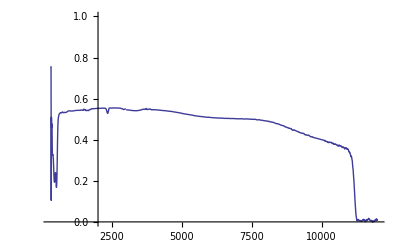

```mathematica
Plot[Abs[trans[sample,v]],{v,301,12000},PlotRange->{{301,12000},{0,1}}]
```

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1.2,0,4},{κ,0.001,0,0.1},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,330,13000,8}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsemi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsemi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsemi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of GaAs : n-doted

```mathematica
d=440*10^-4;sample=8;
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1.2,0,6},{κ,0.001,0,0.1},Compiled->True,DampingFactor->1,MaxIterations->60]},{ν,345,13000,8}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlndot=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientndot=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientndot=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of Si : semi conducting

```mathematica
d=530*10^-4;sample=9;
```

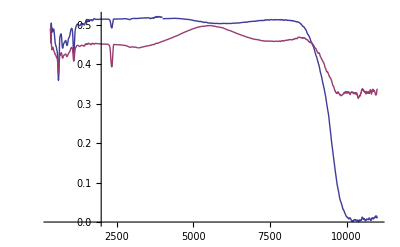

```mathematica
Plot[{trans[sample,ν],reflex[sample,ν]},{ν,350,11000},PlotRange->Full]
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1,0,6},{κ,0.001,-1,1},Compiled->True,DampingFactor->1,MaxIterations->60]},{ν,320,13000,6}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

### Functions

```mathematica
brechzahlFCTsemi=Interpolation[ExponentialMovingAverage[brechzahlsemi,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTsemi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
absorptionFCTsemi=Interpolation[ExponentialMovingAverage[absorptionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
brechzahlFCTndot=Interpolation[ExponentialMovingAverage[brechzahlndot,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTndot=Interpolation[ExponentialMovingAverage[extinktionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
absorptionFCTndot=Interpolation[ExponentialMovingAverage[absorptionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
plots={brechzahlFCTsemi,extinktionFCTsemi,brechzahlFCTndot,extinktionFCTndot};
```

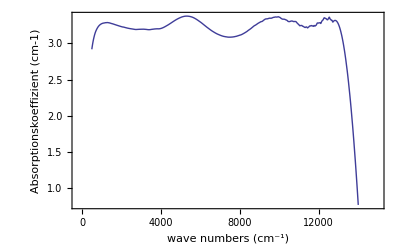
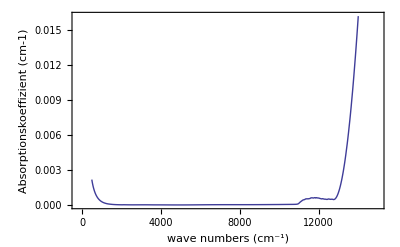
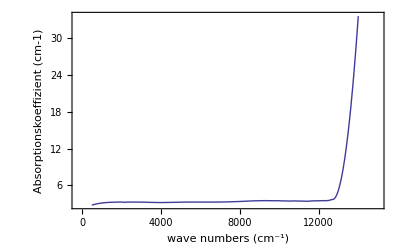
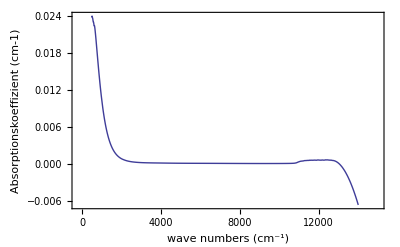

```mathematica
Table[Plot[plots⟦i⟧[x],{x,500,14000},PlotRange->{{-200,15000},Full},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotStyle->Thick,ImageSize->400],{i,1,4}]
```

```mathematica
brechzahlFCTsi=Interpolation[ExponentialMovingAverage[brechzahlsi,average],InterpolationOrder->2];
extinktionFCTsi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsi,average],InterpolationOrder->2];
absorptionFCTsi=Interpolation[ExponentialMovingAverage[absorptionskoeffizientsi,average],InterpolationOrder->2];
```

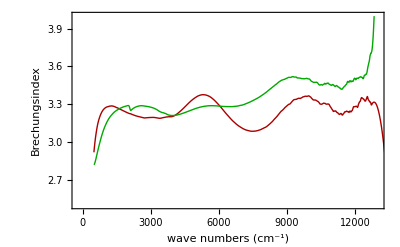

```mathematica
Plot[{brechzahlFCTsemi[x],brechzahlFCTndot[x],brechzahlFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{2.5,4}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Brechungsindex"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

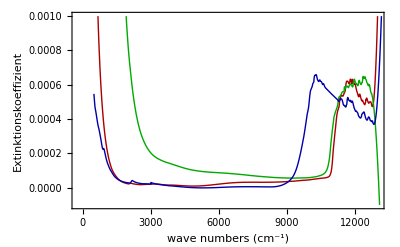

```mathematica
Plot[{extinktionFCTsemi[x],extinktionFCTndot[x],extinktionFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{-0.0001,0.001}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

InterpolatingFunction::dmval: Input value {300.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

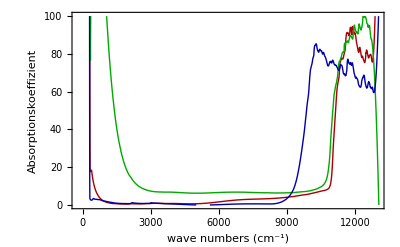

```mathematica
Plot[{absorptionFCTsemi[x],absorptionFCTndot[x],absorptionFCTsi[x]},{x,300,14000},PlotRange->{{-200,13000},{0,100}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

## proper method

#### general

d = 470*10^-4; sample = 7;

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol[sample_,d_]:=Table[{ν,FindRoot[{transth[d,ν]-trans[sample,ν],reflth[d,ν]-reflex[sample,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,500,12000,8}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahl[sample_,d_]:=Table[{sol[sample,d]⟦j,1⟧,n/.sol[sample,d]⟦j,2⟧⟦1⟧},{j,1,Length[Transpose[sol[sample,d]]⟦1⟧]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizient[sample_,d_]:=Table[{sol[sample,d]⟦j,1⟧,κ/.sol[sample,d]⟦j,2⟧⟦2⟧},{j,1,Length[Transpose[sol[sample,d]]⟦1⟧]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizient[sample_,d_]:=Table[{sol[sample,d]⟦j,1⟧,4 π sol[sample,d]⟦j,1⟧*κ/.sol[sample,d]⟦j,2⟧⟦2⟧},{j,1,Length[Transpose[sol[sample,d]]⟦1⟧]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

```mathematica
sample[sample_,d_]:={brechzahl[sample,d],extinktionskoeffizient[sample,d],absorptionskoeffizient[sample,d]}
```

```mathematica
gaasHL=sample[7,470 10^-4]
```

FindRoot::nlnum: The function value {-0.319044 + transth[0.047, 500.], -0.335664 + reflth[0.047, 500.]} is not a list of numbers with dimensions {2} at {n, κ} = {1.1, 0.}.

FindRoot::nlnum: The function value {-0.318598 + transth[0.047, 508.], -0.337013 + reflth[0.047, 508.]} is not a list of numbers with dimensions {2} at {n, κ} = {1.1, 0.}.

FindRoot::nlnum: The function value {-0.315846 + transth[0.047, 516.], -0.337528 + reflth[0.047, 516.]} is not a list of numbers with dimensions {2} at {n, κ} = {1.1, 0.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {-(TagBox[GridBox[{{"{", GridBox[{{TagBox[InterpolatingFunction[{« 1 »}, {« 10 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False]][ν], ν < 3000}, {TagBox[InterpolatingFunction[{« 1 »}, {« 10 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False]][ν], ν > 3000}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]]) + transth[47/1000, ν], -(TagBox[GridBox[{{"{", GridBox[{{TagBox[InterpolatingFunction[{« 1 »}, {« 10 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False]][ν], ν < 4100}, {TagBox[InterpolatingFunction[{« 1 »}, {« 10 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False]][ν], ν > 4100}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]]) + reflth[47/1000, ν]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

$Aborted

$Aborted